## Load data

```mathematica
SetDirectory@NotebookDirectory[];
data=Import["../_Data/supplementary_data.xlsx"];
docs=data[[3]]; (*COLUMN NAMES: {"id","original","place","Latitude","Longitude","year","month","other","vydavatel","vydavatel2"}*)
docs[[2;;All,5]]=Round@docs[[2;;All,5]]; (*round years*)
docList=docs[[2;;All,1]]; (* document names only *)
issuerList=Union[docs[[2;;All,-2]]];  (* issuer names only *)
yearList=Union[docs[[2;;All,5]]];
missing={#,0}&/@Complement[Range[yearList[[1]],yearList[[-1]]],yearList];
(* years without any documents *)
funcList=data[[6,2;;All]]; (* function names only *)

incid=data[[4]]/.""->0;
names=DeleteCases[Drop[incid[[All,2]],1],0];
incid=incid[[2;;Length@names+1,Flatten[Position[incid[[1]],#]&/@docList]]];(* Same ordering as in docs *)
incidFunc=incid;
incid=incid/._String->1;
incid=SparseArray[incid,{Length@names,Length@docList}];
```

### Functions

```mathematica
makeNet[minYear_,maxYear_]:=Module[{selectDoc,selectPos,adjNam,g},
selectDoc=Cases[docs,{x_,_,_,_,year_,_,_,_}:>x/;minYear≤year≤ maxYear];
selectPos=Flatten[Position[docList,#]&/@selectDoc];
adjNam=ArrayRules@SparseArray[incid[[All,selectPos]].Transpose[incid[[All,selectPos]]]-SparseArray@IdentityMatrix[Length[names]],Automatic,0]; (* make adjacency from incidence matrix *)
adjNam=DeleteCases[adjNam,PatternSequence[{x_,x_}->_]];
AppendTo[adjNam,{_,_}->∞];
g=WeightedAdjacencyGraph[SparseArray[adjNam,Length[names]]];
{adjNam,g}
];
```

```mathematica
makeNodes[minYear_,maxYear_]:=Module[{selectDoc,selectPos,adjNam},
selectDoc=Cases[docs,{x_,_,_,_,year_,_,_,_}:>x/;minYear≤year≤ maxYear];
selectPos=Flatten[Position[docList,#]&/@selectDoc];
adjNam=ArrayRules@SparseArray[incid[[All,selectPos]],Automatic,0];
Union@adjNam[[All;;-2,1,1]]
];
```

```mathematica
assortativity[{adjrules_,g_}]:=Module[{rules,edges,adj,degs,strs,m,mw,degAss,strengthAss,leungAss,sums},
degs=DegreeCentrality[g];
If[CompleteGraphQ[Subgraph[g,Flatten@Position[degs,x_/;x≠0]]],
{1.,1.},
rules=Drop[adjrules,-1];
adj=SparseArray[Drop[adjrules,-1]];
rules=Drop[ArrayRules@LowerTriangularize@SparseArray[rules],-1];
strs=Total[adj];
m=Total[degs]/2;
mw=Total[strs]/2;

sums=Transpose[{Times@@degs[[#]],Total@degs[[#]],Total[degs[[#]]^2]}&/@rules[[All,1]]];
degAss=1.(Total[sums[[1]]/m]-Total[sums[[2]]/2/m]^2)/(Total[sums[[3]]/2/m]-Total[sums[[2]]/2/m]^2);
sums=Transpose[{Times@@strs[[#]],Total@strs[[#]],Total[strs[[#]]^2]}&/@rules[[All,1]]];
sums=rules[[All,2]]#&/@sums;
leungAss=1.(Total[sums[[1]]/mw]-Total[sums[[2]]/2/mw]^2)/(Total[sums[[3]]/2/mw]-Total[sums[[2]]/2/mw]^2);
{degAss,leungAss}
]
];
```

```mathematica
entropy[{adjrules_,g_}]:=Module[{rules,edges,adj,degs,strs,m,mw,grw,merw},
adj=SparseArray[Drop[adjrules,-1]];
degs=DegreeCentrality[g];
strs=Total[adj];
m=Total[degs]/2;
mw=Total[strs]/2;

grw=1.Total[degs (Log[degs]/.-∞->0)]/2/m;
merw=Log@Eigenvalues[1.adj,1][[1]];
{grw,merw}
];
```

```mathematica
clustering[{rules_,g_},nodes_]:=Module[{adjrules=rules,adj,degs,strs,n,maxW,weighted,neighs,triangles,tri,norm,res,link},
adjrules[[-1,2]]=0;
nodes=Union@Flatten@Drop[adjrules[[All,1]],-1];
adj=SparseArray[adjrules][[nodes,nodes]];
n=Dimensions[adj][[1]];
degs=DegreeCentrality[g][[nodes]];
strs=Total[adj];
maxW=Max[adj];

weighted=
Table[
neighs=Drop[ArrayRules[adj[[i]]],-1][[All,1,1]];
If[Length@neighs≤ 1,
{0,0,0,0},
triangles=If[link=adj[[#[[1]],#[[2]]]];link==0,0,{#,link}]&/@Tuples[neighs,2];
triangles=Drop[triangles//Union,1];
norm=adj[[i,neighs]];
tri=adj[[i,#[[1,1]]]]adj[[i,#[[1,2]]]]#[[2]]&/@triangles;
{
(*localB*)1/(strs[[i]](degs[[i]]-1)) Total[(adj[[i,#[[1,1]]]]+adj[[i,#[[1,2]]]])/2 If[#[[2]]==0,0,1]&/@triangles],
(*localO*)Total[(tri)^(1/3.)],
(*localZ*)Total[tri]/((Total[norm]^2-Total[norm^2])maxW),
(*localH*)1/(Total[norm]^2 maxW) Total[tri]
}

]
,{i,1,n}];

res=Transpose[weighted];
res[[2]]=res[[2]]/(degs(degs-1)maxW)/.Indeterminate->0;
(*1.Join[{GlobalClusteringCoefficient[g],Mean@LocalClusteringCoefficient[g][[nodes]]},*)1.Mean/@res(*]*)
];
```

### Make networks

```mathematica
wholeNet=makeNet[yearList[[1]],yearList[[-1]]];
nn=VertexCount[wholeNet[[2]]];
ee=EdgeCount[wholeNet[[2]]];
```

```mathematica
(* This one takes some time *)
nets=ParallelTable[makeNet[year,year],{year,yearList}];
```

### Graphics

```mathematica
marker1=Graphics[{EdgeForm[Directive[Thick,RGBColor[0,0,0],Opacity[1]]],White,Disk[]},ImageSize->14];
marker2=Graphics[{EdgeForm[Directive[Thick,RGBColor[1,0,0],Opacity[1]]],RGBColor[1,1,1],Triangle[{{0,0},{1,0},{1/2,√3/2}}]},ImageSize->15];
marker3=Graphics[{RGBColor[0,0,1],Polygon[{{1/2,0},{0,1/2},{1/2,1},{1,1/2}}]},ImageSize->15];
```

```mathematica
(* Overlays for the timeline figures *)
shade=ListPlot[Transpose@{{1248+7/12,1249+8/12},ConstantArray[ee,2]},Joined->True,Filling->Bottom,FillingStyle->Directive[Red,Opacity[0.5]]];
line=ListPlot[{{1230,ee},{1253,ee}},Filling->0,FillingStyle->Directive[Black,Dashed]];
line1=ListPlot[{{1230+0.5,ee},{1253+0.5,ee}},Filling->0,FillingStyle->Directive[Black,Dashed]];
```

## Global network measures

### Assortativity

```mathematica
ass1=Table[ assortativity[net] ,{net,nets}];
(*This might take while *)
assRG=ParallelTable[
g=nets[[j,2]];
degs=DegreeCentrality[g];
sg=Subgraph[g,Flatten@Position[degs,x_/;x≠0]];
rgs={ArrayRules@AdjacencyMatrix[#],#}&/@RandomGraph[{VertexCount[sg],EdgeCount[sg]},100];
Do[
rgs[[i,1,All;;-2,2]]=RandomSample[nets[[j,1]][[All;;-2,2]]]
,{i,1,100}];
Mean@Table[ assortativity[net] ,{net,rgs}]
,{j,1,Length@yearList}];
```

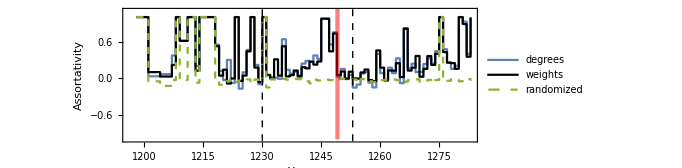

```mathematica
Show[{ListPlot[{Transpose@{yearList,ass1[[All,1]]},Transpose[{yearList,ass1[[All,2]]}](*,Transpose@{yearList,assRG[[All,1]]}*)},Joined->True,InterpolationOrder->0,PlotStyle->{Automatic,Black,Directive[Dashed]},PlotLegends->Placed[{"degrees","weights","randomized"},{0.1,0.2}],Frame->True,PlotRange->{-1.,1.1},AxesOrigin->0, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameLabel->{Style["Year","Arial",12,Black],Style["Assortativity","Arial",14,Black]},ImageSize->505,AspectRatio->1/3],shade,line}]
```

### Entropy

```mathematica
ent1=Table[
m=EdgeCount[net[[2]]];
nn=VertexCount[net[[2]]]-Count[DegreeCentrality[net[[2]]],0];
temptab=Table[
grand=RandomGraph[{nn,m}];
{1.Total[dgs (Log[dgs]/.-∞->0)]/2/m/.dgs->DegreeCentrality[grand],
Log@Eigenvalues[1.AdjacencyMatrix@grand,1][[1]]}
,{100}];
{entropy[net],Around@@#&/@Transpose@{Mean@temptab,StandardDeviation@temptab}}
,{net,nets}];
```

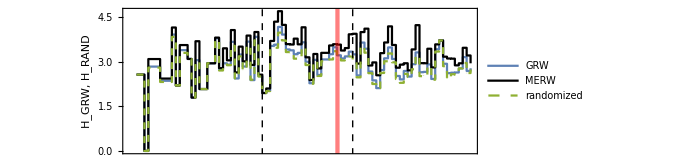

```mathematica
Show[{ListPlot[{Transpose@{yearList,ent1[[All,1,1]]},Transpose@{yearList,ent1[[All,1,2]]},Transpose@{yearList,ent1[[All,2,1]]}},Joined->True,InterpolationOrder->0,PlotStyle->{Automatic,Black,Directive[Dashed]},PlotLegends->Placed[{"GRW","MERW","randomized"},{0.1,0.2}],Frame->True,AxesOrigin->0, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->{{Automatic,Automatic},{None,Automatic}},FrameLabel->{None,Style["H_GRW, H_RAND","Arial",14,Black]},ImageSize->505,AspectRatio->1/3],shade,line}]
```

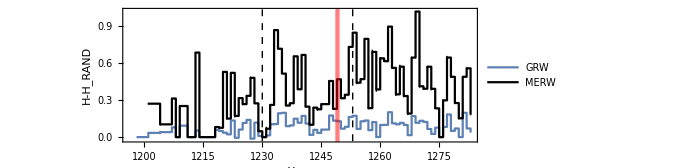

```mathematica
Show[{ListPlot[{Transpose@{yearList,ent1[[All,1,1]]-ent1[[All,2,1]]},Transpose@{yearList,ent1[[All,1,2]]-ent1[[All,2,2]]}},Joined->True,InterpolationOrder->0,PlotStyle->{Automatic,Black},PlotLegends->Placed[{"GRW","MERW"},{0.1,0.7}],Frame->True,AxesOrigin->0, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameLabel->{Style["Year","Arial",12,Black],Style["H-H_RAND","Arial",14,Black]},ImageSize->505,AspectRatio->1/3],shade,line}]
```

### Clustering coefficients

```mathematica
clust2=ParallelTable[
m=EdgeCount[nets[[j,2]]];
nn=Length[makeNodes[yearList[[j]],yearList[[j]]]];
rgs={ArrayRules@AdjacencyMatrix[#],#}&/@RandomGraph[{nn,m},100];
Do[
rgs[[i,1,All;;-2,2]]=RandomSample[nets[[j,1]][[All;;-2,2]]]
,{i,1,100}];
Quiet[
Join[clustering[nets[[j]],makeNodes[yearList[[j]],yearList[[j]]]],Mean@Table[ clustering[net,Range[nn]] ,{net,rgs}]]
]
,{j,1,Length@yearList}];
```

```mathematica
clust1=Table[
g=nets[[j,2]];
sg=Subgraph[g,makeNodes[yearList[[j]],yearList[[j]]]];
rgs=RandomGraph[{VertexCount[sg],EdgeCount[sg]},100];
{1.GlobalClusteringCoefficient[sg],
1.Mean@LocalClusteringCoefficient[sg],Mean@Table[ 1.GlobalClusteringCoefficient[net] ,{net,rgs}],Mean@Table[1. Mean@LocalClusteringCoefficient[net] ,{net,rgs}]}
,{j,1,Length@yearList}];
```

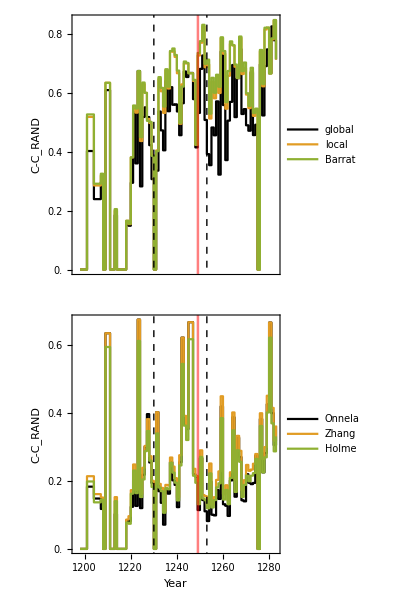

```mathematica
Grid[{{
Show[{ListPlot[{Transpose@{yearList,clust1[[All,1]]-clust1[[All,3]]},Transpose@{yearList,clust1[[All,2]]-clust1[[All,4]]},
Transpose@{yearList,clust2[[All,1]]-clust2[[All,5]]}},Joined->True,InterpolationOrder->0,PlotStyle->{Black,Automatic,Automatic},PlotLegends->Placed[{"global","local","Barrat"},{0.09,0.77}],Frame->True,AxesOrigin->0, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->{{Table[{t,t,{0.01,0}},{t,0,0.8,0.2}],Table[{t,"",{0.01,0}},{t,0,0.8,0.2}]},{Table[{t,"",{0.01,0}},{t,1200,1280,20}]~Join~Table[{t,"",{0.005,0}},{t,1200,1280,5}],Automatic}},FrameLabel->{None,Style["C-C_RAND","Arial",14,Black]},ImageSize->Automatic->460,AspectRatio->1/3],shade,line}]
},
{Show[{ListPlot[{Transpose@{yearList,clust2[[All,2]]-clust2[[All,6]]},Transpose@{yearList,clust2[[All,3]]-clust2[[All,7]]},Transpose@{yearList,clust2[[All,4]]-clust2[[All,8]]}},Joined->True,InterpolationOrder->0,PlotStyle->{Black,Automatic,Automatic},PlotLegends->Placed[{"Onnela","Zhang","Holme"},{0.09,0.77}],Frame->True,AxesOrigin->0, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->{{Table[{t,t,{0.01,0}},{t,0,0.8,0.2}],Table[{t,"",{0.01,0}},{t,0,0.8,0.2}]},{Automatic,Automatic}},FrameLabel->{Style["Year","Arial",12,Black],Style["C-C_RAND","Arial",14,Black]},ImageSize->Automatic->460,AspectRatio->1/3],shade,line}]
}},Spacings->{0,-0.2},Alignment->Right]
```

### Mean path length

```mathematica
pathlen=Table[
{adjrules,g}=net;
degs=DegreeCentrality[g];
sg=Subgraph[g,Flatten@Position[degs,x_/;x≠0]];
baseline=((Log[VertexCount[sg]]-EulerGamma)/(Log@Mean@Cases[degs,x_/;x>0])+1/2);
rgs=RandomGraph[{VertexCount[sg],EdgeCount[sg]},100];
temp1=Mean@Table[
degs=DegreeCentrality[rg];
 1.Total@Total[(GraphDistanceMatrix[rg]/.∞->0)/(VertexCount[rg]-1)/VertexCount[rg]]/((Log[VertexCount[sg]]-EulerGamma)/(Log@Mean@Cases[degs,x_/;x>0])+1/2) ,{rg,rgs}];
{temp=Total@Total[(GraphDistanceMatrix[sg]/.∞->0)/(VertexCount[sg]-1)/VertexCount[sg]],temp/baseline,temp1}
,{net,nets}];
```

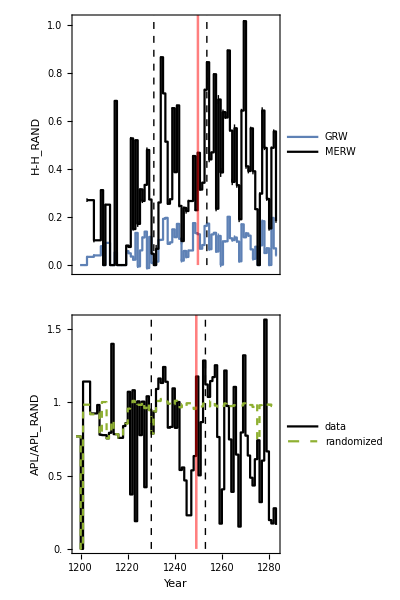

```mathematica
Grid[{{Show[{ListPlot[{Transpose@{yearList,ent1[[All,1,1]]-ent1[[All,2,1]]},Transpose@{yearList,ent1[[All,1,2]]-ent1[[All,2,2]]}},Joined->True,InterpolationOrder->0,PlotStyle->{Automatic,Black},PlotLegends->Placed[{"GRW","MERW"},{0.1,0.7}],Frame->True,AxesOrigin->0, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->{{Automatic,Automatic},{Table[{t,"",{0.01,0}},{t,1200,1280,20}]~Join~Table[{t,"",{0.005,0}},{t,1200,1280,5}],Automatic}},FrameLabel->{None,Style["H-H_RAND","Arial",14,Black]},ImageSize->Automatic->460,AspectRatio->1/3],shade,line}]},
{
Show[{ListPlot[{Transpose@{yearList,pathlen[[All,2]]},Transpose@{yearList,pathlen[[All,3]]}},Joined->True,InterpolationOrder->0,PlotStyle->{Black,Directive[ColorData[97][3],Dashed]},Frame->True,
PlotLegends->Placed[{"data","randomized"},{0.17,0.2}],AxesOrigin->{yearList[[1]],1}, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->{{Table[i,{i,0,1.5,0.5}],Table[{i,""},{i,0,1.5,0.5}]},{Automatic,Automatic}},FrameLabel->{Style["Year","Arial",12,Black],Style["APL/APL_RAND","Arial",14,Black]},ImageSize->Automatic->460,AspectRatio->1/3],shade,line}]
}},Spacings->{0,-0.2},Alignment->Right]
```